# Detector Rules

This tutorial defines the functions and derivatives to implement detectors in DALI for gravitational waves

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

```mathematica
PacletDirectoryLoad["/Users/felipe/Documents/GitHub"]
<<FelipeBarbosa`SymDALI`
```

{/Users/felipe/Documents/GitHub}

## Overview

The gravitational wave strain is defined by:

```mathematica
HoldForm[strain === (SubPlus[F][α, δ, GMST] SubPlus[h] + Subscript[F, x][α, δ, GMST] Subscript[h, x]) Exp[-I 2 π f Δt]]
HoldForm[SubPlus[h] === (1+Cos[ι]^2)/2 h]
HoldForm[Subscript[h, x] === -I Cos[ι] h]
```

strain===(F_+[α,δ,GMST] h_++F_x[α,δ,GMST] h_x) Exp[-ⅈ 2 π f Δt]

h_+===1/2 (1+Cos[ι]^2) h

h_x===-ⅈ Cos[ι] h

Where, Δt is the time interval for the GW to propagate from the detector to the Earth's center (assuming speed of light velocity), GMST is the Greenwich mean sideral time of detection, α is the right ascension and δ is the declination. The implementation of detectors consists in rewriting the strain as:

```mathematica
HoldForm[strain === S1[α, sinδ, cosι] h]
HoldForm[S1[α, sinδ, cosι] === (SubPlus[F][α, δ, GMST] (1+cosι^2)/2 - Subscript[F, x][α, δ, GMST]  I cosι ) Exp[-I 2 π f Δt]]
```

strain===S1[α,sinδ,cosι] h

S1[α,sinδ,cosι]===(1/2 F_+[α,δ,GMST] (1+cosι^2)-F_x[α,δ,GMST] ⅈ cosι) Exp[-ⅈ 2 π f Δt]

and finding the derivatives of S1[α, sinδ, cosι] analogously to what was done in IMRPhenomD Rules. First we recognize that  F_+  ≡ e_(+,ij) D_ij ∧ F_x ≡ e_(x,ij) D_ij, where D_ij is the usual detector tensor D_ij ≡ 1/2 ( nx_i nx_j - ny_i ny_j). Meaning that we can factor D_ij and keep a function  that returns a matrix:

```mathematica
HoldForm[(SubPlus[e][α, sinδ, GMST] (1+cosι^2)/2 - I cosι Subscript[e, x][α, sinδ, GMST]) Exp[-I 2 π f Δt]]
```

(1/2 e_+[α,sinδ,GMST] (1+cosι^2)-ⅈ cosι e_x[α,sinδ,GMST]) Exp[-ⅈ 2 π f Δt]

with the understanding that e_+ and e_x are matrix functions. The polarization tensors in the geocentric frame are defined by similarity transformations:

```mathematica
polarizationTensors[α_, sinδ_, GMST_] := Module[
	{θ, δ, ϕ = α - GMST, eplus, ecross, R1, R2, T, D, eplusGeoFrame, ecrossGeoFrame},
	(*Polarization frame tensors*)
	θ= π/2 - δ;

    eplus = {{1,0,0}, {0,-1,0}, {0,0,0}};
    ecross = {{0,1,0}, {1,0,0}, {0,0,0}};
    
    R1 = List[
        {-Sin[ϕ], Cos[ϕ], 0}, (*\hat{ϕ} decomposed in \hat{e}_i*)
        {Cos[θ] Cos[ϕ], Cos[θ] Sin[ϕ], -Sin[θ]}, (*\hat{θ} decomposed in \hat{e}_i*)
        {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]} (*\hat{r}decomposed in \hat{e}_i*)
    ];
	
	R1 = (R1//.{Sin[δ] -> sinδ, Cos[δ]-> Sqrt[1- sinδ^2]})//FullSimplify;


    R2 = RotationMatrix[-ψ, {0,0,1}];
    T = R2 . R1//Simplify;
    
	eplusGeoFrame = (Tᵀ . eplus . T);
    ecrossGeoFrame = (Tᵀ.ecross.T);

]
```

Meaning that our Function can be written as

```mathematica
HoldForm[Transpose[T].(SubPlus[e] (1+cosι^2)/2 - I cosι Subscript[e, x]).T Exp[-I 2 π f Δt]]
```

Transpose[T].(1/2 e_+ (1+cosι^2)-ⅈ cosι e_x).T Exp[-ⅈ 2 π f Δt]

Now

```mathematica
Δt[detectorposition_, α_, sinδ_, gmst_] := Module[
	{δ, ϕ = α-gmst,θ, r, c = UnitConvert["SpeedOfLight"][[1]]},
	
	θ = π/2 - δ;
	
	r = FromSphericalCoordinates[{1, θ, ϕ}]//.{Sin[δ] -> sinδ, Cos[δ] -> √(1- sinδ^2)};
	
	-(detectorposition.r)/c
]
```

where the detector position is given in meters following the LIGO convention. All of these considerations lead to the definition:

```mathematica
(*make some trace operator that commutes with D:*)
Unprotect@Tr
Tr/: D[Tr[x_], y___] := Tr[D[x,y]];
Tr[0] := 0 (*This shoudn't happen but the derivatives of order 3 or higher in cosι give you 0 straightfoward, 
instead of Dot[something, 0, somethingelse] in any case you can do this with trace so that it is accounted for.
*)

{SymRules["detectors"], NRules["detectors"]} = Module[
	{δt, δ, θ, ϕ = α-gmst, matrix1, matrix2, delta},

	θ = π/2 - δ;

	delta = Δt[detectorPosition, α, sinδ, gmst];
	
	matrix1 = List[
        {-Sin[ϕ], Cos[ϕ], 0}, 
        {Cos[θ] Cos[ϕ], Cos[θ] Sin[ϕ], -Sin[θ]},
        {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]} 
    ];
	
	matrix1 = (matrix1//.{Sin[δ] -> sinδ, Cos[δ]-> Sqrt[1- sinδ^2]})//FullSimplify;

	matrix2 = RotationMatrix[-ψ, {0,0,1}];

	Unevaluated@DerivativeRules[
		{S1, {α, sinδ, cosι, ψ}, 5},

		$Block[
		{{m1, m2,m3,m4, Δ}},

		
		(*NOTE THAT WE ONLY DECLARE VARIABLES THAT APPEAR IN DERIVATIVES*)
		Δ[α_, sinδ_] := DELTA;
		m1[α_, sinδ_] := MATRIX1;
		m2[ψ_] := MATRIX2;
		m3[α_, sinδ_] := TMATRIX1;
		m4[ψ_] := TMATRIX2;

		(*T = m2.m1:*)
		Dot[
			(m3[α, sinδ].m4[ψ].(1/2 (1+cosι^2) eplus - I cosι ecross).m2[ψ].m1[α, sinδ]) Exp[-I 2 π f Δ[α, sinδ]],
			Transpose[detectorTensor]
		]//Tr
	],
	"KeepDefs" -> {eplus -> {{1,0,0}, {0,-1,0}, {0,0,0}}, ecross -> {{0,1,0}, {1,0,0}, {0,0,0}}}
]//.{DELTA ->delta, MATRIX1 -> matrix1, MATRIX2 -> matrix2, TMATRIX1-> Transpose[matrix1], TMATRIX2 -> Transpose[matrix2]}

]; (*Insert the correct trace operator*)
```

{Tr}

"symbolic Derivatives: "  0.094348

"sym derivatives -> $x and explicit derivatives: "  0.062524

"Make Block functions: "  0.005996

"Looking for numbers: "  0.630961

```mathematica
(ByteCount/@NRules["detectors"])//{Total[#], Max[#]}&
```

{5590200,209536}

## Checking

Now we shall check our definitions for the antenna pattern function. We will be using bilby to write the Python representation of

```mathematica
HoldForm[Transpose[T].(SubPlus[e] (1+cosι^2)/2 - I cosι Subscript[e, x]).T Exp[-I 2 π f Δt]]
```

Transpose[T].(1/2 e_+ (1+cosι^2)-ⅈ cosι e_x).T Exp[-ⅈ 2 π f Δt]

contracted with the detector tensor D_ij. We will be working with the detector 'H1':

```mathematica
python = StartExternalSession["Python"];
ExternalEvaluate[python, {"import numpy as np", "import bilby"}]
ExternalEvaluate[python, "detector = bilby.gw.detector.get_empty_interferometer('H1')"]
```

{Null,Null}

```mathematica
pythonFunction = ExternalFunction[python, "def function(ra, dec, gps, psi, cosiota, f):
	Fp = detector.antenna_response(ra = ra, dec = dec,  time = gps, psi =psi, mode = 'plus')
	Fc = detector.antenna_response(ra = ra, dec = dec,  time = gps, psi =psi, mode = 'cross')
	deltaT = detector.time_delay_from_geocenter(ra = ra, dec=dec, time = gps )
	deltaT = np.exp(-1j*2*np.pi*f*deltaT)
	result = (Fp*0.5*(1+cosiota**2) - complex(0,1)*cosiota*Fc)*deltaT

	return result
"]
```

ExternalFunction[…]

We need a function  that converts GPS to GMST for our defs:

```mathematica
GMST = ExternalFunction[python, "
from astropy.time import Time
def gmst_accurate(gps_time):
    gmst = Time(gps_time, format='gps', scale='utc',
                location=(0, 0)).sidereal_time('mean').rad
    return gmst"
];
```

We will need the detector tensor and position of H1, that can be taken from here:

```mathematica
{H1Tensor, H1pos} = With[{
	nx = {-0.22389266154, 0.79983062746,0.55690487831}, ny = {-0.91397818574, 0.02609403989, -0.40492342125},
	pos = {-2.16141492636 10^6, -3.83469517889 10^6,4.60035022664 10^6}
},
	{
		0.5 (nx⊗nx - ny⊗ny),
		pos
	}

];
```

Finally, we define a function that takes the detector position and tensor and returns our scalar quantity:

```mathematica
(*Add the detec as a variable and remove the HoldForm from the definition:*)
MMAfunction1[α_, sinδ_, ψ_, gmst_, cosι_,  detectorPosition_, detectorTensor_, f_] = NRules["detectors"][[1,2]];
DownValues[MMAfunction1] = DownValues[MMAfunction1]//.HoldForm[x_] :> x;
```

Now we compare:

```mathematica
CompareFunctions := Module[
	{gps = RandomReal[{10^8, 10^9}], α= RandomReal[{0, 2 π}], δ = RandomReal[{-π/2, π/2}], ψ = RandomReal[{0,π}], cosι = RandomReal[{-1,1}], 
	f = Range[20, 4000, 1], pythonF, MMA, gmst},

	pythonF = pythonFunction[α, δ, gps, ψ, cosι, #]&/@f;
	gmst = GMST[gps];
	MMA = MMAfunction1[α, Sin[δ], ψ, gmst, cosι, H1pos, H1Tensor, #]&/@f;
	{MMA, pythonF}
]
```

```mathematica
test = CompareFunctions;
```

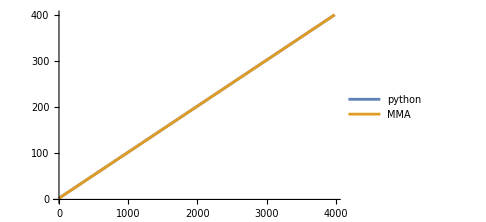
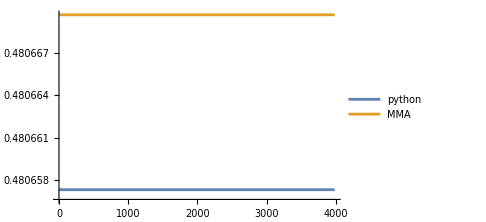

```mathematica
Module[
	{pythonArg, MMAArg, pythonABS, MMAABS},
	pythonArg = test[[2]]//Arg//ResourceFunction["PhaseUnwrap"];
	MMAArg = test[[1]]//Arg//ResourceFunction["PhaseUnwrap"];
	
	pythonABS = test[[2]]//Abs;
	MMAABS = test[[1]]//Abs;

	{
		ListLinePlot[{pythonArg, MMAArg}, ImageSize->Medium, PlotLegends->{"python", "MMA"}],
		ListLinePlot[{pythonABS, MMAABS}, ImageSize->Medium, PlotLegends->{"python", "MMA"}, PlotRange->All]
	}
] (*There is a small overestimation of the absolute value from Mathematica, but it seems good enough*)
```

## Compiling and Exporting

We need 2 changes before proceeding: add extra variables to the function definitions and remove the Exp[x_] from function definitions for every function with more than one derivative. there are 4 variables to add: (gmst, f,  detectorPosition, detectorTensor), none of which are being derived. So:

```mathematica
NRules["detectors"][[2,1]]
```

$D[{1,0,0,0},S1][α_,sinδ_,cosι_,ψ_]

```mathematica
newSymRules = <||>; newNRules = <||>;

{newSymRules["detectors"], newNRules["detectors"]} = Module[
	{addVars,headsNR, headsSR},

	(*Make a function to change the heads:*)
	addVars[x_]/; (AtomQ[x[[0]]]) := Join[
		x, 
		x[[0]][gmst_, detectorPosition_, detectorTensor_, f_]
	];
	
	addVars[x_] := Module[
		{newHead = x[[0]]}, 
		newHead[[1]] = Join[newHead[[1]], {0,0,0,0}];
		Join[
			newHead@@x, 
			newHead[gmst_, detectorPosition_, detectorTensor_, f_]
		]
	];
	
	headsNR = addVars/@(NRules["detectors"][[All, 1]]);
	headsSR = addVars/@(SymRules["detectors"][[All, 1]]);

	(*Return the new lists of rules:*)
	{
		Thread@Rule[headsSR, SymRules["detectors"][[All,2]]],
		Thread@Rule[headsNR, NRules["detectors"][[All,2]]]
	}
];
```

Again, export SymRules is straightforward:

```mathematica
With[{
   	directory = FileNameJoin[ParentDirectory[NotebookDirectory[], 3], "DerivativeRules/Detectors/SymRules"]},
  	SaveSymRules[{newSymRules, "SymRules"}, directory]
  ];
```

Apparently ```Tr```is not compilable, so I will just change to its explicit definition in this case:

```mathematica
(*change Tr -> to the def of Trace:*)
newNRules["detectors"] = newNRules["detectors"]//.Tr[x_] :> Sum[x[[i,i]], {i,1,3}];
```

Now, we need the CompiledFunctions:

```mathematica
(*make a function to pass the HoldForm[...] functions to the CLibraryFunction:*)
PassFunction[expr_] := Unevaluated@CLibraryFunction[
	{
		{α, _Real}, {sinδ, _Real}, {cosι, _Real}, {ψ, _Real},{gmst, _Real}, {detectorPosition, _Real, 1},
		{detectorTensor, _Real, 2}, {f, _Real}
	}, 
	expr

]/.HoldForm[x_] -> x

CFunctions = Association[
	"detectors" -> MapAt[PassFunction, newNRules["detectors"], {All, 2}]
];
```

α, Sin[δ], ψ, gmst, cosι, #, H1pos, H1Tensor

Now, we just save them:

```mathematica
With[ 
	{directory = FileNameJoin[ParentDirectory[NotebookDirectory[],3], "DerivativeRules/Detectors/NRules"]},
	SaveNRules[CFunctions, directory]
];
```

## Checking compiled functions

```mathematica
Clear[iSymRules, iNRules]
{iSymRules, iNRules} = DerivativeRulesLoad["Detectors"];
```

```mathematica
CompareFunctions := Module[
	{gps = RandomReal[{10^8, 10^9}], α= RandomReal[{0, 2 π}], δ = RandomReal[{-π/2, π/2}], ψ = RandomReal[{0,π}], cosι = RandomReal[{-1,1}], 
	f = Range[20, 4000, 100], pythonF, MMA, gmst},

	pythonF = pythonFunction[α, δ, gps, ψ, cosι, #]&/@f;
	gmst = GMST[gps];

	MMA = iNRules["detectors"][[1,2]][α, Sin[δ], cosι, ψ, gmst, H1pos, H1Tensor, #]&/@f;
	{MMA, pythonF}
]
```

```mathematica
test = CompareFunctions;
```

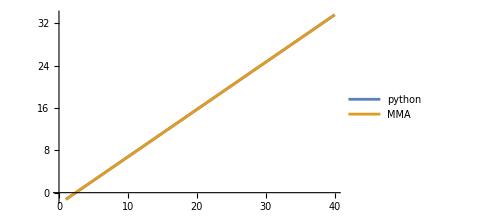
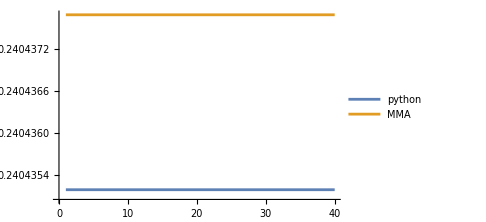

```mathematica
Module[
	{pythonArg, MMAArg, pythonABS, MMAABS},
	pythonArg = test[[2]]//Arg//ResourceFunction["PhaseUnwrap"];
	MMAArg = test[[1]]//Arg//ResourceFunction["PhaseUnwrap"];
	
	pythonABS = test[[2]]//Abs;
	MMAABS = test[[1]]//Abs;

	{
		ListLinePlot[{pythonArg, MMAArg}, ImageSize->Medium, PlotLegends->{"python", "MMA"}],
		ListLinePlot[{pythonABS, MMAABS}, ImageSize->Medium, PlotLegends->{"python", "MMA"}]
	}
] (*There is a small overestimation of the absolute value from Mathematica, but it seems good enough*)
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

SymDALI

SampleTools`Private`

SymDALI/tutorial/Detector-Rules

### Keywords

$Aborted